# Ex.1

```mathematica
Zklass=10
Zklass2=10*9
```

10

90

```mathematica
Zbose=Zklass+0.5*Zklass2
```

55.

```mathematica
Zfermi=0.5*Zklass2
```

45.

```mathematica
pklass=0
pbose=10/Zbose
pfermi=0
```

0

0.181818

0

# Ex.2

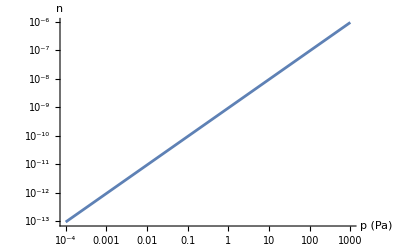

```mathematica
k:=
dE:=
T:=
Zint:=223
Z:=Zint*Exp[-dE/(k*T)]
n[p_]:=Z*p/(1+Z*p)
LogLogPlot[n[p],{p,0.0001,1000},AxesLabel->{"p (Pa)","n"}]
```

# Ex.3

```mathematica
ClearAll["Global`*"]
eqn:=p==R*T/(V-b)-a/V^2
sol=Solve[{eqn,D[eqn,V],D[eqn,{V,2}]},{p,T,V}][[1]]
```

{p→a/(27 b^2),T→(8 a)/(27 b R),V→3 b}

```mathematica
a:=
R:=
b:=
Tc=T/.sol//UnitConvert
pc=p/.sol
Vc=V/.sol//N
```

640.636 K

21478. kPa

93. cm^3/mol

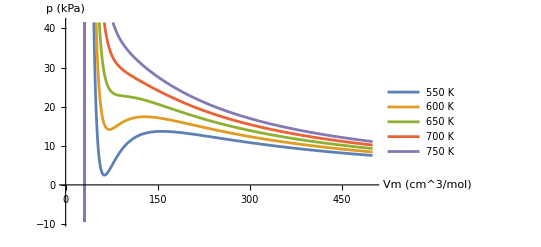

```mathematica
p[T_,V_]:=1/1000R*T*/(V*-b)-1/1000a/V^2*
Plot[{p[550,V],p[600,V],p[650,V],p[700,V], p[750,V]},{V,1, 500},AxesLabel->{"Vm (cm^3/mol)","p (kPa)"},PlotLegends->{"550 K","600 K", "650 K","700 K", "750 K"},PlotRange->{Automatic,Automatic}]
```

Nachdem das Volumen nicht negativ sein kann, geht das Integral auch nicht zu 0.